```mathematica
(* PREDEF *)
Get[NotebookDirectory[]<>"dmbog_std_mathematica_v1.wl"];
```

Imported dmbog_std_mathematica.wl

```mathematica
(* Считываем процесс & параметры задачи *)
Std■Header2@"Параметры задачи"
solution=Import[NotebookDirectory[]<>"../temp/sde_test_params/process.json"];
params=Import[NotebookDirectory[]<>"../temp/sde_test_params/params.json"]

Ξiters="iteration"/.solution;
Ξt="t"/.solution;
ΞW="W"/.solution//Flatten;
preciseΞX="sol"/.solution//Flatten;
```

-- Параметры задачи --

{callback_freq→1,seed→17,t1→0,t2→1,tau→0.01,y1→{0}}

-- Аналитическое решение --

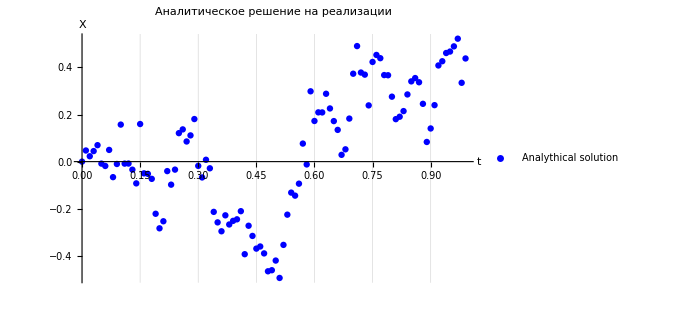

```mathematica
(* Аналитическое решение *)
Std■Header2@"Аналитическое решение"

plotPrecise=ListPlot[Transpose@{Ξt,preciseΞX},PlotStyle->Blue,AxesLabel->{"t","X"},PlotLegends->{"Analythical solution"},PlotLabel->"Аналитическое решение на реализации",Evaluate@Std■PlotStyle]
```

- Метод Эйлера-Мураямы -

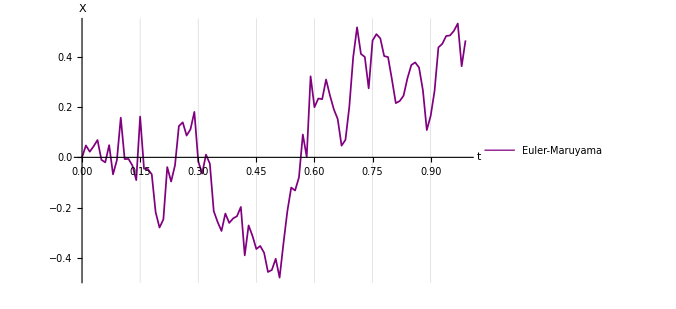

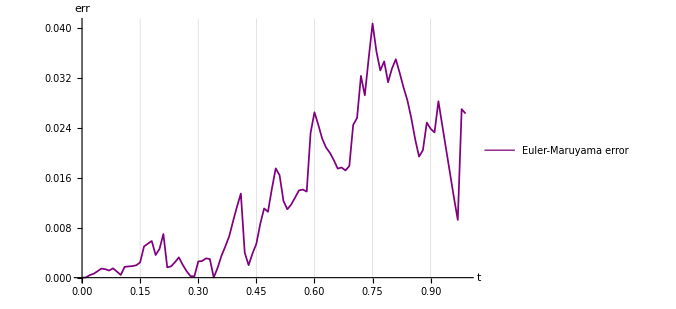

/home/georgehaldane/Documents/PROJECTS/CPP/rkdg_solver/proj/scripts/images/sde_test/euler_maruyama_sol.pdf

/home/georgehaldane/Documents/PROJECTS/CPP/rkdg_solver/proj/scripts/images/sde_test/euler_maruyama_err.pdf

- Модифицированный Метод Милштейна -

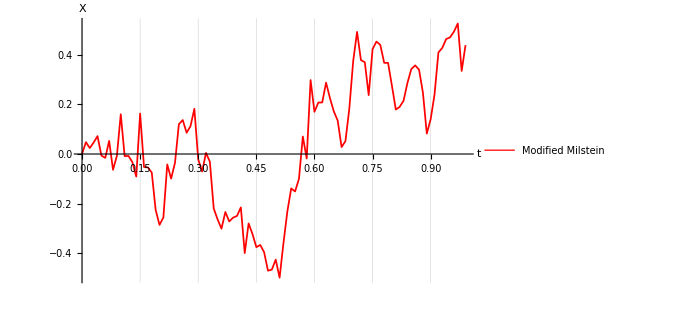

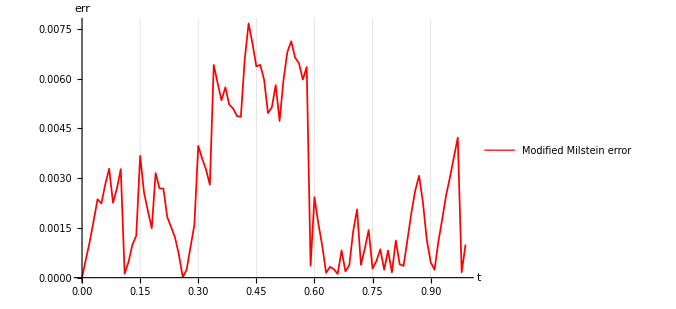

/home/georgehaldane/Documents/PROJECTS/CPP/rkdg_solver/proj/scripts/images/sde_test/modified_milstein_sol.pdf

/home/georgehaldane/Documents/PROJECTS/CPP/rkdg_solver/proj/scripts/images/sde_test/modified_milstein_err.pdf

```mathematica
(* Метод Эйлера-Мураямы *)
Std■Header3@"Метод Эйлера-Мураямы"
solution=Import[NotebookDirectory[]<>"../temp/sde_test_solution/euler_maruyama.json"];
EulerMaruyamaΞX="y"/.solution//Flatten;

styleEM={PlotStyle->Directive[Thickness@0.0025,Purple]};
plotEM=ListLinePlot[Transpose@{Ξt,EulerMaruyamaΞX},Evaluate@styleEM,AxesLabel->{"t","X"},PlotLegends->{"Euler-Maruyama"},Evaluate@Std■PlotStyle]
errEM=Table[Abs[preciseΞX⟦k⟧-EulerMaruyamaΞX⟦k⟧],{k,1,Length@Ξt}];
plotErrEM=ListLinePlot[Transpose@{Ξt,errEM},Evaluate@styleEM,AxesLabel->{"t","err"},PlotLegends->{"Euler-Maruyama error"},Evaluate@Std■PlotStyle]

Export[NotebookDirectory[]<>"images/sde_test/euler_maruyama_sol.pdf",plotEM]
Export[NotebookDirectory[]<>"images/sde_test/euler_maruyama_err.pdf",plotErrEM]

(* Модифицированный Метод Милштейна *)
Std■Header3@"Модифицированный Метод Милштейна"
solution=Import[NotebookDirectory[]<>"../temp/sde_test_solution/modified_milstein.json"];
ModifiedMilsteinΞX="y"/.solution//Flatten;

styleMM={PlotStyle->Directive[Thickness@0.0025,Red]};
plotMM=ListLinePlot[Transpose@{Ξt,ModifiedMilsteinΞX},Evaluate@styleMM,AxesLabel->{"t","X"},PlotLegends->{"Modified Milstein"},Evaluate@Std■PlotStyle]
errMM=Table[Abs[preciseΞX⟦k⟧-ModifiedMilsteinΞX⟦k⟧],{k,1,Length@Ξt}];
plotErrMM=ListLinePlot[Transpose@{Ξt,errMM},Evaluate@styleMM,AxesLabel->{"t","err"},PlotLegends->{"Modified Milstein error"},Evaluate@Std■PlotStyle]

Export[NotebookDirectory[]<>"images/sde_test/modified_milstein_sol.pdf",plotMM]
Export[NotebookDirectory[]<>"images/sde_test/modified_milstein_err.pdf",plotErrMM]
```

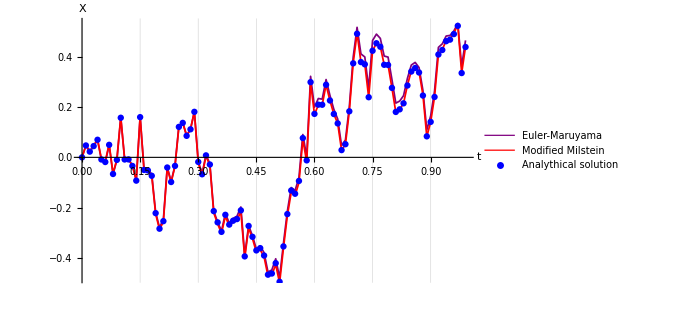

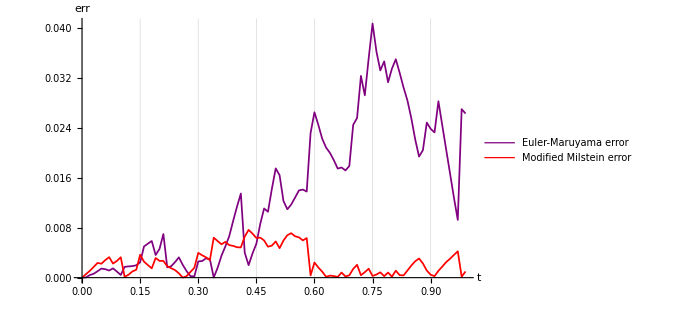

/home/georgehaldane/Documents/PROJECTS/CPP/rkdg_solver/proj/scripts/images/sde_test/joined_sol.pdf

/home/georgehaldane/Documents/PROJECTS/CPP/rkdg_solver/proj/scripts/images/sde_test/joined_err.pdf

```mathematica
(* Сравнение результатов, оценки точности *)
plotJoinedSol=Show[plotEM,plotMM,plotPrecise]
ploJoinedErr=Show[plotErrEM,plotErrMM]

Export[NotebookDirectory[]<>"images/sde_test/joined_sol.pdf",plotJoinedSol]
Export[NotebookDirectory[]<>"images/sde_test/joined_err.pdf",ploJoinedErr]
```

```mathematica
EulerMaruyamaRelativeNorm=Norm[EulerMaruyamaΞX-preciseΞX]/Norm[preciseΞX]
ModifiedMilsteinRelativeError=Norm[ModifiedMilsteinΞX-preciseΞX]/Norm[preciseΞX]
```

0.0663044

0.0129194